# State Transitions - Time Dependent

```mathematica
SetDirectory[NotebookDirectory[]];
FCL={20,10,5};
CIAL={80,70,68};
F2L={200,30,20};
F3L={3400,420,60};
FML={100,200,50};
FSL={500,150,300};
MPL={50,8500,20};
O2L={1.0,0.481333,1.22222};

(* Helper function to get easy access to list entry *)
at[list_, index_]:= list[[index]]
nestedAt[list_, index_, index2_]:=at[at[list, index], index2]

RegFunction[k_, n_, SP_, C_, x_]:=k/(1+Exp[n*(x-SP)])+C
getk23[list_]:=Module[{fccase,ciacase,f2case,f3case},fccase=RegFunction[0.293708,-0.248768,15.105,0,FC[t]];
ciacase=RegFunction[0.227484,-0.652642,71.4237,0,CIA[t]];
f2case=RegFunction[0.226644,-0.130635,37.073,0,F2[t]];
f3case=RegFunction[0.226655,-0.00362872,674.652,0,F3[t]];
Switch[list,FCL,fccase,CIAL,ciacase,F2L,f2case,F3L,f3case]]
getkO2[list_]:=Module[{fscase},fscase=RegFunction[95.3616,-0.0134783,258.284,0,FS[t]];
Switch[list,FSL,fscase]]
getkCIA[list_]:=Module[{o2case,fmcase,mpcase},o2case=RegFunction[4.661,-8.87757,1.41475,0.418826,O2[t]];
fmcase=RegFunction[5.50768,0.0387998,0.991932,0.41756,FM[t]];
mpcase=RegFunction[3.006,0.0690787,3.09565,0.42,MP[t]];
Switch[list,O2L,o2case,FML,fmcase,MPL,mpcase]]
getkCYT[list_]:=Module[{f2case,ciacase,f3case,fccase},f2case=RegFunction[16.6101,0.159447,7.90727,2.62995,F2[t]];
ciacase=RegFunction[1557.4,0.744197,59.1271,2.62967,CIA[t]];
f3case=RegFunction[5.00448,0.00537466,0.991933,2.62995,F3[t]];
fccase=RegFunction[2.15854,1.00162,8.74028,2.62992,FC[t]];
Switch[list,F2L,f2case,CIAL,ciacase,F3L,f3case,FCL,fccase]]
getkMIT[list_]:=Module[{fscase},fscase=RegFunction[168.632,0.022031,0.991933,0.538779,FS[t]];
Switch[list,FSL,fscase]]
getkMP[list_]:=Module[{o2case,mpcase,fmcase},o2case=RegFunction[4.1828,8.89003,0.130172,0,O2[t]];
mpcase=RegFunction[0.176593,-0.0142367,376.877,0,MP[t]];
fmcase=RegFunction[0.931282,-0.0587368,224.854,0.00105854,FM[t]];
Switch[list,O2L,o2case,MPL,mpcase,FML,fmcase]]
getkVAC[list_]:=Module[{f2case,ciacase,f3case,fccase},f2case=RegFunction[2.99975,-0.076787,56.8973,0,F2[t]];
ciacase=RegFunction[3.67913,-0.377767,76.0689,0,CIA[t]];
f3case=RegFunction[3.04175,-0.00213037,1396.83,0,F3[t]];
fccase=RegFunction[2.88787,-0.679725,14.0134,0.160357,FC[t]];
Switch[list,F2L,f2case,CIAL,ciacase,F3L,f3case,FCL,fccase]]
cases ={{FCL,FML,FCL,FSL,FCL,FSL,FML},{FCL,FML,FCL,FSL,FCL,FSL,MPL},{FCL,FML,FCL,FSL,F2L,FSL,FML},{FCL,FML,FCL,FSL,F2L,FSL,MPL},{FCL,FML,FCL,FSL,F3L,FSL,FML},{FCL,FML,FCL,FSL,F3L,FSL,MPL},{FCL,FML,CIAL,FSL,FCL,FSL,FML},{FCL,FML,CIAL,FSL,FCL,FSL,MPL},{FCL,FML,CIAL,FSL,F3L,FSL,FML},{FCL,FML,CIAL,FSL,F3L,FSL,MPL},{FCL,FML,F3L,FSL,F3L,FSL,FML},{FCL,FML,F3L,FSL,F3L,FSL,MPL},{FCL,MPL,FCL,FSL,FCL,FSL,FML},{FCL,MPL,FCL,FSL,FCL,FSL,MPL},{FCL,MPL,FCL,FSL,CIAL,FSL,FML},{FCL,MPL,FCL,FSL,F2L,FSL,FML},{FCL,MPL,FCL,FSL,F2L,FSL,MPL},{FCL,MPL,FCL,FSL,F3L,FSL,FML},{FCL,MPL,FCL,FSL,F3L,FSL,MPL},{FCL,MPL,CIAL,FSL,FCL,FSL,MPL},{FCL,MPL,CIAL,FSL,F3L,FSL,MPL},{FCL,MPL,F3L,FSL,F3L,FSL,FML},{FCL,MPL,F3L,FSL,F3L,FSL,MPL},{FCL,O2L,FCL,FSL,FCL,FSL,FML},{FCL,O2L,FCL,FSL,FCL,FSL,MPL},{FCL,O2L,FCL,FSL,CIAL,FSL,FML},{FCL,O2L,FCL,FSL,CIAL,FSL,MPL},{FCL,O2L,FCL,FSL,F2L,FSL,FML},{FCL,O2L,FCL,FSL,F2L,FSL,MPL},{FCL,O2L,FCL,FSL,F3L,FSL,FML},{FCL,O2L,FCL,FSL,F3L,FSL,MPL},{FCL,O2L,F3L,FSL,F3L,FSL,FML},{FCL,O2L,F3L,FSL,F3L,FSL,MPL},{CIAL,FML,FCL,FSL,FCL,FSL,FML},{CIAL,FML,FCL,FSL,FCL,FSL,MPL},{CIAL,FML,FCL,FSL,F3L,FSL,FML},{CIAL,FML,FCL,FSL,F3L,FSL,MPL},{CIAL,FML,CIAL,FSL,FCL,FSL,FML},{CIAL,FML,CIAL,FSL,FCL,FSL,MPL},{CIAL,FML,CIAL,FSL,F3L,FSL,FML},{CIAL,FML,CIAL,FSL,F3L,FSL,MPL},{CIAL,FML,F3L,FSL,FCL,FSL,FML},{CIAL,FML,F3L,FSL,FCL,FSL,MPL},{CIAL,FML,F3L,FSL,F3L,FSL,FML},{CIAL,FML,F3L,FSL,F3L,FSL,MPL},{CIAL,MPL,FCL,FSL,FCL,FSL,FML},{CIAL,MPL,FCL,FSL,FCL,FSL,MPL},{CIAL,MPL,FCL,FSL,CIAL,FSL,FML},{CIAL,MPL,FCL,FSL,F3L,FSL,FML},{CIAL,MPL,FCL,FSL,F3L,FSL,MPL},{CIAL,MPL,CIAL,FSL,FCL,FSL,MPL},{CIAL,MPL,CIAL,FSL,F3L,FSL,MPL},{CIAL,MPL,F3L,FSL,FCL,FSL,FML},{CIAL,MPL,F3L,FSL,FCL,FSL,MPL},{CIAL,MPL,F3L,FSL,F3L,FSL,FML},{CIAL,MPL,F3L,FSL,F3L,FSL,MPL},{CIAL,O2L,FCL,FSL,FCL,FSL,FML},{CIAL,O2L,FCL,FSL,FCL,FSL,MPL},{CIAL,O2L,FCL,FSL,CIAL,FSL,FML},{CIAL,O2L,FCL,FSL,CIAL,FSL,MPL},{CIAL,O2L,FCL,FSL,F3L,FSL,FML},{CIAL,O2L,FCL,FSL,F3L,FSL,MPL},{CIAL,O2L,F3L,FSL,FCL,FSL,FML},{CIAL,O2L,F3L,FSL,FCL,FSL,MPL},{CIAL,O2L,F3L,FSL,F3L,FSL,FML},{CIAL,O2L,F3L,FSL,F3L,FSL,MPL},{F2L,FML,FCL,FSL,FCL,FSL,FML},{F2L,FML,FCL,FSL,FCL,FSL,MPL},{F2L,FML,FCL,FSL,F2L,FSL,FML},{F2L,FML,FCL,FSL,F2L,FSL,MPL},{F2L,FML,FCL,FSL,F3L,FSL,FML},{F2L,FML,FCL,FSL,F3L,FSL,MPL},{F2L,FML,CIAL,FSL,FCL,FSL,FML},{F2L,FML,CIAL,FSL,FCL,FSL,MPL},{F2L,FML,CIAL,FSL,F2L,FSL,FML},{F2L,FML,CIAL,FSL,F2L,FSL,MPL},{F2L,FML,CIAL,FSL,F3L,FSL,FML},{F2L,FML,CIAL,FSL,F3L,FSL,MPL},{F2L,FML,F2L,FSL,FCL,FSL,FML},{F2L,FML,F2L,FSL,FCL,FSL,MPL},{F2L,FML,F2L,FSL,F2L,FSL,FML},{F2L,FML,F2L,FSL,F2L,FSL,MPL},{F2L,FML,F2L,FSL,F3L,FSL,FML},{F2L,FML,F2L,FSL,F3L,FSL,MPL},{F2L,FML,F3L,FSL,F2L,FSL,MPL},{F2L,FML,F3L,FSL,F3L,FSL,MPL},{F2L,MPL,FCL,FSL,FCL,FSL,FML},{F2L,MPL,FCL,FSL,FCL,FSL,MPL},{F2L,MPL,FCL,FSL,CIAL,FSL,FML},{F2L,MPL,FCL,FSL,F2L,FSL,FML},{F2L,MPL,FCL,FSL,F2L,FSL,MPL},{F2L,MPL,FCL,FSL,F3L,FSL,FML},{F2L,MPL,FCL,FSL,F3L,FSL,MPL},{F2L,MPL,CIAL,FSL,FCL,FSL,MPL},{F2L,MPL,CIAL,FSL,F3L,FSL,MPL},{F2L,MPL,F2L,FSL,FCL,FSL,FML},{F2L,MPL,F2L,FSL,FCL,FSL,MPL},{F2L,MPL,F2L,FSL,CIAL,FSL,FML},{F2L,MPL,F2L,FSL,F2L,FSL,FML},{F2L,MPL,F2L,FSL,F2L,FSL,MPL},{F2L,MPL,F2L,FSL,F3L,FSL,FML},{F2L,MPL,F2L,FSL,F3L,FSL,MPL},{F2L,MPL,F3L,FSL,F2L,FSL,MPL},{F2L,MPL,F3L,FSL,F3L,FSL,MPL},{F2L,O2L,FCL,FSL,FCL,FSL,FML},{F2L,O2L,FCL,FSL,FCL,FSL,MPL},{F2L,O2L,FCL,FSL,CIAL,FSL,FML},{F2L,O2L,FCL,FSL,CIAL,FSL,MPL},{F2L,O2L,FCL,FSL,F2L,FSL,FML},{F2L,O2L,FCL,FSL,F2L,FSL,MPL},{F2L,O2L,FCL,FSL,F3L,FSL,FML},{F2L,O2L,FCL,FSL,F3L,FSL,MPL},{F2L,O2L,F2L,FSL,FCL,FSL,FML},{F2L,O2L,F2L,FSL,FCL,FSL,MPL},{F2L,O2L,F2L,FSL,CIAL,FSL,FML},{F2L,O2L,F2L,FSL,CIAL,FSL,MPL},{F2L,O2L,F2L,FSL,F2L,FSL,FML},{F2L,O2L,F2L,FSL,F2L,FSL,MPL},{F2L,O2L,F2L,FSL,F3L,FSL,FML},{F2L,O2L,F2L,FSL,F3L,FSL,MPL},{F2L,O2L,F3L,FSL,F2L,FSL,MPL},{F2L,O2L,F3L,FSL,F3L,FSL,MPL},{F3L,FML,FCL,FSL,FCL,FSL,FML},{F3L,FML,FCL,FSL,FCL,FSL,MPL},{F3L,FML,FCL,FSL,F3L,FSL,FML},{F3L,FML,FCL,FSL,F3L,FSL,MPL},{F3L,FML,CIAL,FSL,FCL,FSL,FML},{F3L,FML,CIAL,FSL,FCL,FSL,MPL},{F3L,FML,CIAL,FSL,F3L,FSL,FML},{F3L,FML,CIAL,FSL,F3L,FSL,MPL},{F3L,FML,F3L,FSL,F3L,FSL,MPL},{F3L,MPL,FCL,FSL,FCL,FSL,FML},{F3L,MPL,FCL,FSL,FCL,FSL,MPL},{F3L,MPL,FCL,FSL,CIAL,FSL,FML},{F3L,MPL,FCL,FSL,F3L,FSL,FML},{F3L,MPL,FCL,FSL,F3L,FSL,MPL},{F3L,MPL,CIAL,FSL,FCL,FSL,MPL},{F3L,MPL,CIAL,FSL,F3L,FSL,MPL},{F3L,MPL,F3L,FSL,F3L,FSL,MPL},{F3L,O2L,FCL,FSL,FCL,FSL,FML},{F3L,O2L,FCL,FSL,FCL,FSL,MPL},{F3L,O2L,FCL,FSL,CIAL,FSL,FML},{F3L,O2L,FCL,FSL,CIAL,FSL,MPL},{F3L,O2L,FCL,FSL,F3L,FSL,FML},{F3L,O2L,FCL,FSL,F3L,FSL,MPL},{F3L,O2L,F3L,FSL,F3L,FSL,MPL}};
```

```mathematica
simulateTimeTransition[startStateValue_, caseId_, startIron_, startkisu_] := Module[{alpha, kisu, Kcyt, Kmit, Kvac, Kcia, Kisu, KresO2, KF2, O2SP, OXYGEN, CARBON, kres, k23, kcia, kvac, caseValue, IRON, kmit, kcyt, kO2, kmp, Rcyt, Rmit, Rvac, Rcia, Risu, Rmp, RO2, Rres, R23, fcyt, fmit, fvac, ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, eqns, s},
caseValue = caseId;
IRON = startIron;
kisu =startkisu; 
alpha = 0.000222188885555*kisu + 0.00185188888889;

Kcyt = 10;
Kmit = 20;
Kvac = 20;
Kcia = 20; 
Kisu = 100;
KresO2 = 1;
KF2 = 200; 
O2SP = 1; 
OXYGEN = 100; 
 CARBON = 100; 
kres =36.363636363636363636364;




k23 = getk23[nestedAt[cases, caseValue, 1]];
kcia = getkCIA[nestedAt[cases, caseValue, 2]];
kvac =  getkVAC[nestedAt[cases, caseValue, 3]];
kmit = getkMIT[nestedAt[cases, caseValue, 4]];
kcyt = getkCYT[nestedAt[cases, caseValue, 5]];
kO2 = getkO2[nestedAt[cases, caseValue, 6]];
kmp = getkMP[nestedAt[cases, caseValue, 7]];
Print[k23,kcia,kvac,kmit,kcyt,kO2,kmp];
Rcyt = kcyt * IRON/(Kcyt + IRON);
Rmit = kmit * FC[t]/(Kmit + FC[t]);
Rvac = kvac * FC[t]/(Kvac + FC[t]);
Rcia = kcia * FC[t]/(Kcia+FC[t]);
Risu = kisu * FM[t]/(Kisu + FM[t])*O2SP/(O2SP+O2[t]);
Rmp = kmp * FM [t]* O2[t];
RO2 = kO2 * (OXYGEN- O2[t]); 
Rres = kres * FS[t] * O2[t]/(KresO2 + O2[t]);
R23 = k23 * F2[t] /(KF2+F2[t])*OXYGEN;
fcyt = 0.8;
fmit = 0.1;
fvac = 0.1; 
ode1=FC'[t]==Rcyt-Rvac-Rmit-Rcia-alpha*FC[t];
ode2=CIA'[t]==Rcia-alpha*CIA[t];
ode3=F2'[t]==fcyt/fvac*Rvac-R23-alpha*F2[t];
ode4=F3'[t]==R23-alpha*F3[t];
ode5=FM'[t]==fcyt/fmit*Rmit-Risu-Rmp-alpha*FM[t];
ode6=FS'[t]==Risu-alpha*FS[t];
ode7=MP'[t]==Rmp-alpha*MP[t];
ode8=O2'[t]==RO2-Rmp-Rres-alpha*O2[t];
eqns = {ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, FC[0] ==FCL[[startStateValue]], CIA[0]==CIAL[[startStateValue]], F2[0] == F2L[[startStateValue]], F3[0]==F3L[[startStateValue]], FM[0]==FML[[startStateValue]],MP[0]== MPL[[startStateValue]], FS[0]==FSL[[startStateValue]], O2[0]== O2L[[startStateValue]]};
s = NDSolve[eqns,{FC, CIA, F2, F3, FM, FS, MP, O2},{t, 0, 500000}];
<<NumericalCalculus`;
s]
```

```mathematica
s = simulateTimeTransition[1, 1, 1, 6.666]
```

{{FC→InterpolatingFunction[…],CIA→InterpolatingFunction[…],F2→InterpolatingFunction[…],F3→InterpolatingFunction[…],FM→InterpolatingFunction[…],FS→InterpolatingFunction[…],MP→InterpolatingFunction[…],O2→InterpolatingFunction[…]}}

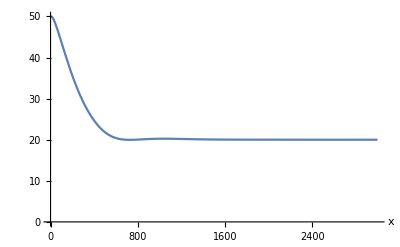

```mathematica
s = simulateTimeTransition[1, 1, 1, 6.666];
stopTime = 3000; 
Plot[Evaluate[MP[x]/. s],{x,0,stopTime},PlotRange->{0,50}, AxesLabel->Automatic]
```

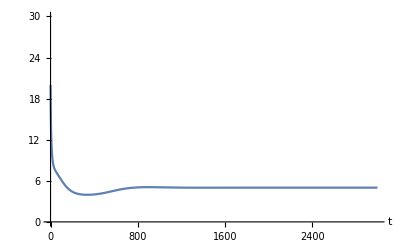

```mathematica
Plot[Evaluate[FC[t]/. s],{t,0,   stopTime},PlotRange->{0,30}, AxesLabel->Automatic]
```

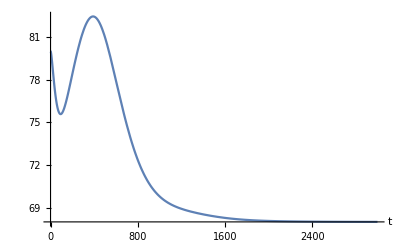

```mathematica
Plot[Evaluate[CIA[t]/. s],{t,0,stopTime},PlotRange->Automatic, AxesLabel->Automatic]
```

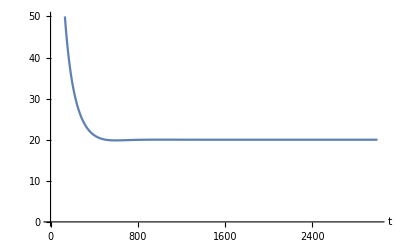

```mathematica
Plot[Evaluate[F2[t]/. s],{t,0,stopTime},PlotRange->{0,50}, AxesLabel->Automatic]
```

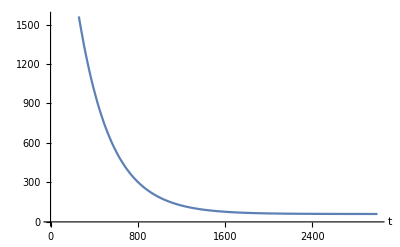

```mathematica
Plot[Evaluate[F3[t]/. s],{t,0,stopTime},PlotRange->Automatic, AxesLabel->Automatic]
```

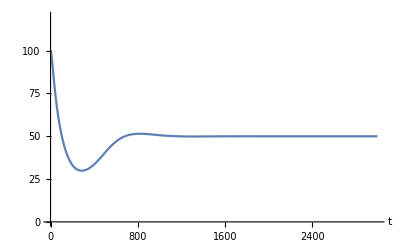

```mathematica
Plot[Evaluate[FM[t]/. s],{t,0,stopTime},PlotRange->{0,120}, AxesLabel->Automatic]
```

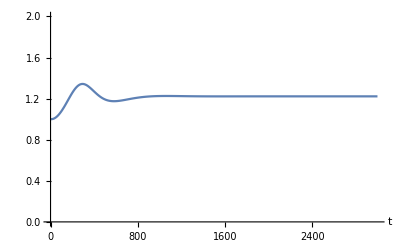

```mathematica
Plot[Evaluate[O2[t]/. s],{t,0,stopTime},PlotRange->{0,2}, AxesLabel->Automatic]
```

Since the range of the plots is quite large, we can normalize each component function relative to the maximum component size.

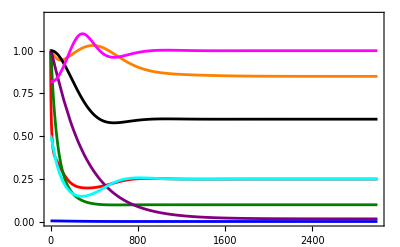

```mathematica
getNormalizedPlot[caseId_, startState_, startIron_, startkisu_, maxtime_, linethickness_, maxYValue_]:= Module[{s,a,c,e,d,f,g,h,i},
s = simulateTimeTransition[startState, caseId, startIron, startkisu];

a = Plot[Rescale[Evaluate[MP[t]/. s],{0,Max[MPL]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Blue,Thickness[linethickness]}];

c = Plot[Rescale[Evaluate[FC[t]/. s],{0, Max[FCL]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Red,Thickness[linethickness]}];

d = Plot[Rescale[Evaluate[F2[t]/. s],{0, Max[F2L]}], {t,0, maxtime}, PlotRange->{0,30}, PlotStyle->{RGBColor[0,0.5,0],Thickness[linethickness]}];e = Plot[Rescale[Evaluate[CIA[t]/. s],{0,Max[CIAL]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Orange,Thickness[linethickness]}];f = Plot[Rescale[Evaluate[F3[t]/. s],{0, Max[F3L]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Purple,Thickness[linethickness]}];

g = Plot[Rescale[Evaluate[FS[t]/. s],{0, Max[FSL]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Black,Thickness[linethickness]}];
h = Plot[Rescale[Evaluate[FM[t]/. s],{0,Max[FML]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Cyan,Thickness[linethickness]}];
i = Plot[Rescale[Evaluate[O2[t]/. s],{0,Max[O2L]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Magenta,Thickness[linethickness]}];

 Show[a,c,d,e,f,g,h,i,PlotRange-> {{0,3000},{0.0, maxYValue}}, BaseStyle->{PrintPrecision->2},Axes->False,Frame->{{True,False},{True,False}} 
]];
(**Legended[wdplot,  LineLegend[{Blue, Red, RGBColor[0,0.5,0], Orange, Purple,  Black ,Cyan, Magenta}, {"MP","FC","F2","CIA","F3","FS","FM","O2"}]]**)
wd = getNormalizedPlot[1, 1, 1, 6.666, 3000, 0.005,1.2]
```

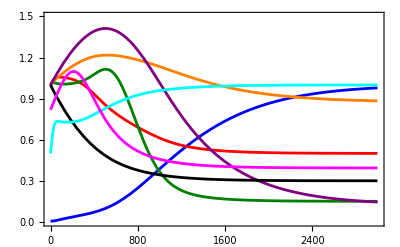

```mathematica
wy = getNormalizedPlot[1, 1, 40, 6.666/10.0, 3000, 0.005,1.5]
```

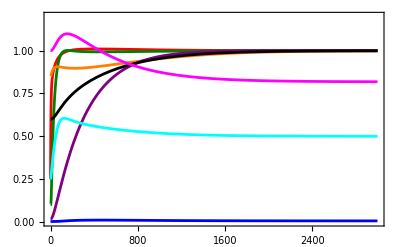

```mathematica
dw = getNormalizedPlot[1,3,40,6.666,3000,0.005,1.2]
```

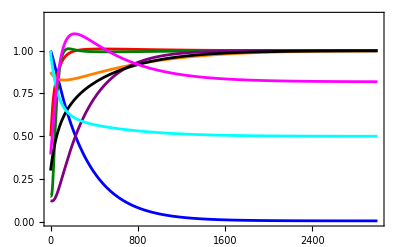

```mathematica
yw = getNormalizedPlot[1,2,40,6.666,3000,0.005,1.2]
```

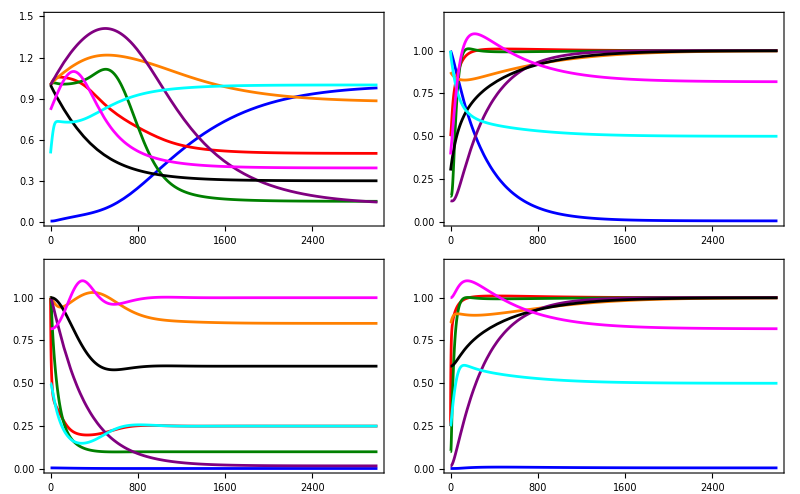

```mathematica
superfigure = GraphicsGrid[{{wy, yw},{wd,dw}},Spacings->{0,0}, Alignment->Center]
```

```mathematica
axisLabels = Labeled[superfigure,{"Time (minutes)","Normalized Component Concentration"},{Bottom,Left},RotateLabel->True];
finalImage = Legended[axisLabels,  LineLegend[{Blue, Red, RGBColor[0,0.5,0], Orange, Purple,  Black ,Cyan, Magenta}, {"MP","FC","F2","CIA","F3","FS","FM","O2"}]];
Show[finalImage]
```

-Graphics-Time (minutes)Normalized Component Concentration

```mathematica
Export["../SavedFigures/WYWDTime.tiff",finalImage, ImageResolution->500]
```

../SavedFigures/WYWDTime.tiff